Computing the eigenvalues of H using numerical approach

### The q-ratio is properly chosen and avoids strong oscillating behavior of λ near certain points across q-interval

```mathematica
matEl[n_,m_,e_,v_]:=Piecewise[{{n*e,n-m==0},{Sqrt[m+1]Sqrt[m+2](-v),n-m==2},{Sqrt[m]Sqrt[m-1](-v),n-m==-2 }}];
Hmat02[n_,e_,v_]:=Table[Table[matEl[2(i-1),2(j-1),e,v],{j,1,n}],{i,1,n}];
Hmat13[n_,e_,v_]:=Table[Table[matEl[2i+1,2j+1,e,v],{j,0,n-1}],{i,0,n-1}];
```

```mathematica
boson0[n_,q_]:=Hmat02[n,1,q];
boson1[n_,q_]:=Hmat13[n,1,q];
```

Solutions of the matrix Hamiltonian

```mathematica
sol0[n_,q_]:=Sort[Eigenvalues[boson0[n,q]],Smaller];
sol1[n_,q_]:=Sort[Eigenvalues[boson1[n,q]],Smaller];
```

```mathematica
sol0[10,1]
```

{Root41.3Root[103382496+604499552 #1-41678064 #1^2-140711040 #1^3+12473040 #1^4+3910032 #1^5-436968 #1^6-9120 #1^7+2430 #1^8-90 #1^9+#1^10&,10]41.25019734957156,Root28.4Root[103382496+604499552 #1-41678064 #1^2-140711040 #1^3+12473040 #1^4+3910032 #1^5-436968 #1^6-9120 #1^7+2430 #1^8-90 #1^9+#1^10&,9]28.36192142691424,Root19.1Root[103382496+604499552 #1-41678064 #1^2-140711040 #1^3+12473040 #1^4+3910032 #1^5-436968 #1^6-9120 #1^7+2430 #1^8-90 #1^9+#1^10&,8]19.129175394578912,Root12.0Root[103382496+604499552 #1-41678064 #1^2-140711040 #1^3+12473040 #1^4+3910032 #1^5-436968 #1^6-9120 #1^7+2430 #1^8-90 #1^9+#1^10&,7]12.047781596494492,Root-11.6Root[103382496+604499552 #1-41678064 #1^2-140711040 #1^3+12473040 #1^4+3910032 #1^5-436968 #1^6-9120 #1^7+2430 #1^8-90 #1^9+#1^10&,1]-11.649592349407092,Root6.55Root[103382496+604499552 #1-41678064 #1^2-140711040 #1^3+12473040 #1^4+3910032 #1^5-436968 #1^6-9120 #1^7+2430 #1^8-90 #1^9+#1^10&,6]6.554016220947679,Root-5.83Root[103382496+604499552 #1-41678064 #1^2-140711040 #1^3+12473040 #1^4+3910032 #1^5-436968 #1^6-9120 #1^7+2430 #1^8-90 #1^9+#1^10&,2]-5.834315454808082,Root2.41Root[103382496+604499552 #1-41678064 #1^2-140711040 #1^3+12473040 #1^4+3910032 #1^5-436968 #1^6-9120 #1^7+2430 #1^8-90 #1^9+#1^10&,5]2.409780909343012,Root-2.10Root[103382496+604499552 #1-41678064 #1^2-140711040 #1^3+12473040 #1^4+3910032 #1^5-436968 #1^6-9120 #1^7+2430 #1^8-90 #1^9+#1^10&,3]-2.0987766498859894,Root-0.170Root[103382496+604499552 #1-41678064 #1^2-140711040 #1^3+12473040 #1^4+3910032 #1^5-436968 #1^6-9120 #1^7+2430 #1^8-90 #1^9+#1^10&,4]-0.17018844374872263}

```mathematica
N[sol0[10,1][[1]]]
```

41.2502

```mathematica
N[lambda13Q[10,2,1]]
```

-6.49645

Evolution of λ with the ratio q

```mathematica
lambda02Q[n_,id_,q_]:=sol0[n,q][[id]];
lambda13Q[n_,id_,q_]:=sol1[n,q][[id]];
```

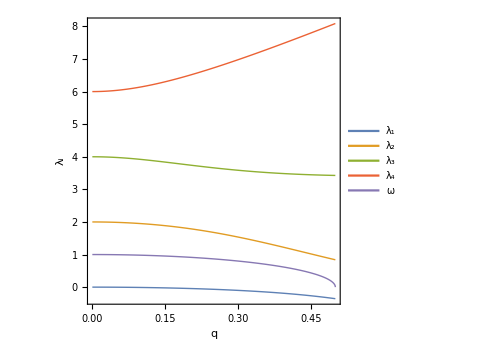

```mathematica
Plot[{lambdaQ[4,1,p],lambdaQ[4,2,p],lambdaQ[4,3,p],lambdaQ[4,4,p],Sqrt[1-4p^2]},{p,0,0.5},AspectRatio->1,Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],LabelStyle->{Black,20,Bold,FontFamily->"Times New Roman"},FrameLabel->{"q",Subscript["λ","i"]},PlotLegends->Placed[{"λ_1","λ_2","λ_3","λ_4","ω"},{0.15,0.7}],ImageSize->Medium,PlotStyle->Thick]
```